# The Parlour (1998) Model

## 3 - step case

## Parameters

```mathematica
v=11/2; a=6; b=5;
```

```mathematica
p[β_]=PDF[UniformDistribution[{0,2}],β]
```

Piecewise[{{1/2, 0≤β≤2}, {0, True}}]

```mathematica
pr[β_]=CDF[UniformDistribution[{0,2}],β]
```

Piecewise[{{β/2, 0≤β≤2}, {1, β>2}, {0, True}}]

## Compute probabilities of events at t=3

At the last step, there is no point in sending a limit order at t=T because there is no chance it will be filled.  Thus the only choices at t=T=3 are Market Order or Do Nothing.

Conditional on being a seller (S), probability of market sell (MS) is given by

```mathematica
pr[b/v]
```

5/11

```mathematica
N[b/v]
```

0.909091

```mathematica
pMS[3]=1/2 pr[b/v]
```

5/22

```mathematica
pMB[3]=pMS[3]
```

5/22

The probability of doing nothing is just

```mathematica
pN[3]=1-pMB[3]-pMS[3]
```

6/11

```mathematica
N[{pMB[3],pMS[3]}]
```

{0.227273,0.227273}

This looks consistent with Figure 12.3 of Hasbrouck.

## Compute probablities of events at t=2

### Book empty

Wlog, focus on seller and consider benefits of alternative actions assuming the ask side of the book is empty.  If there is an existing sell order, it cannot be optimal to submit a limit sell order because such an order will not be executed.

```mathematica
benLS[β_]=(a-β v)pMB[3];
benMS[β_]=b-β v;
```

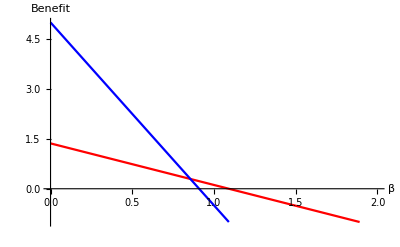

```mathematica
Plot[{benLS[β],benMS[β]},{β,0,2},PlotStyle->{Red,Blue},PlotRange->{-1,5},AxesLabel->{"β","Benefit"}]
```

So, MS is optimal when β ∈(0, x1) with

```mathematica
x1=β/.Flatten[Solve[benMS[β]==benLS[β],β]]
```

160/187

or, solving by hand,

```mathematica
x1=(b - a pMB[3])/(v(1-pMB[3]))
```

160/187

```mathematica
pr[160/187]
```

80/187

```mathematica
N[x1]
```

0.855615

LS is optimal when x1 < β < x2 with

```mathematica
x2=β/.Flatten[Solve[benLS[β]==0,β]]
```

12/11

```mathematica
N[x2]
```

1.09091

Doing nothing is optimal otherwise. Thus

```mathematica
pMS[2]=pr[x1]
```

80/187

```mathematica
pLS[2]=(pr[x2]-pr[x1])
```

2/17

```mathematica
pMB[2]=pMS[2]; pLB[2]=pLS[2];
```

### 1 share in book

If the ask side of the book has quantity, a limit sell order placed at t-2 will not be executed so the problem reduces to the step-3 case.  MS if β < 10/11.  It follows that we need to increase the size of the state space to include quantity on the ask side of the book.

### Expand notation

```mathematica
pMS[0,0][2]=pMB[0,0][2]=pMS[1,0][2]=pMB[0,1][2]=40/187;
```

```mathematica
pLS[0,0][2]=pLB[0,0][2]=pLS[1,0][2]=pLB[0,1][2]=1/17;
```

```mathematica
pLS[0,1][2]=pLB[0,1][2]=0;
```

```mathematica
pMS[0,1][2]=pMB[1,0][2]=5/22;
```

```mathematica
pLB[0,1][2]=pMB[1,0][2]=5/22;
```

```mathematica
pMS[0,0][2]+pMB[0,0][2]+pLS[0,0][2]+pLB[0,0][2]
```

6/11

```mathematica
pMS[0,1][2]+pMB[0,1][2]+pLS[0,1][2]+pLB[0,1][2]
```

125/187

## Compute probablities of events at t=1

By assumption this is the first step so there is no quantity in the order book.  Again assume a seller.

If trader places LS at t=1, the book will be (0,1) at t=2.  The probability of a market buy at times t = 2 or t = 3 is then given by:

```mathematica
pFill[1]=pMB[0,1][2]+(1-pMB[0,1][2])*pMB[3]
```

95/242

```mathematica
benLS[β_]=(a-β v)pFill[1];
benMS[β_]=b-β v;
```

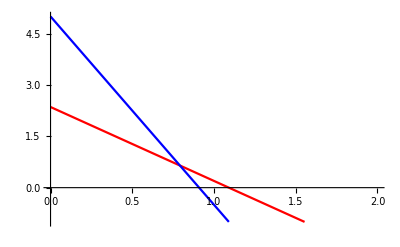

```mathematica
Plot[{benLS[β],benMS[β]},{β,0,2},PlotStyle->{Red,Blue},PlotRange->{-1,5}]
```

So, MS when β < x1 with

```mathematica
x1=β/.Flatten[Solve[benMS[β]==benLS[β],β]]
```

1280/1617

LS is optimal when x1 < β < x2 with

```mathematica
x2=β/.Flatten[Solve[benLS[β]==0,β]]
```

12/11

Doing nothing is optimal otherwise. Thus

```mathematica
pMS[1]=1/2 pr[x1]
```

320/1617

which is the probability trader 1 being a seller times the probability of MS given that time 1 trader is a seller.

```mathematica
pLS[1]=1/2(pr[x2]-pr[x1])
```

11/147

same story as previous line.

## Expected book size

Sell quantity at t = 2 is given by probability of LS at t = 1.

```mathematica
eS[2]=pLS[1]
```

11/147

Sell quantity at t = 3 is given by probability of LS at t = 1 plus probability of LS at t=2 (which means there was no limit sell at t=1.

```mathematica
es[3]=pLS[1]+(1-pLS[1])pLS[0,0][2]
```

19/147

These computations appear to agree with Hasbrouck Figure 12.2